# Problem set 2.1

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

Remove::rmnsm: There are no symbols matching "Global`*".

a) For σ taking each of the values {−1,0,1}, plot a set of representative trajectories, for example using StreamPlot[] or NDSolve[] in Mathematica. Classify the fixed point in each of the cases and write your classification in the plots. Upload the three separate plots in one .pdf or .png file.

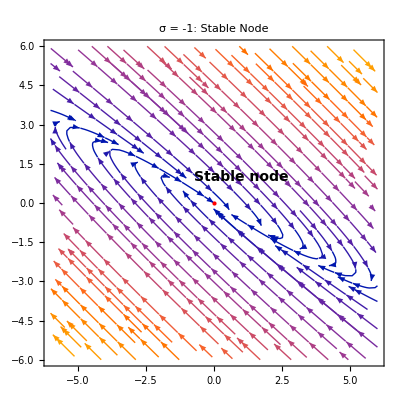

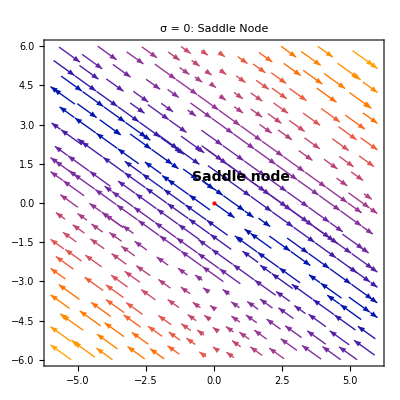

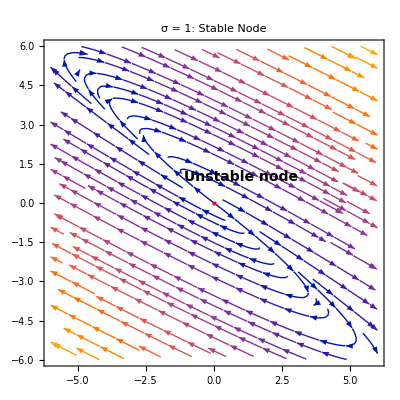

```mathematica
A[sigma_] := {{sigma + 3, 4}, {-9/4, sigma - 3}};
  Ax[sigma_, x_, y_] := (sigma + 3) x + 4 y;
  Ay[sigma_, x_, y_] := (-9/4) x + (sigma - 3) y;

  s1 = StreamPlot[
   {Ax[-1, x, y], Ay[-1, x, y]},
   {x, -6, 6}, {y, -6, 6},
   StreamStyle -> Thick,
   PlotLabel -> "σ = -1: Stable Node",
   Epilog -> {
    Red, PointSize[Large], Point[{0, 0}],  
    Black, 
    Text[Style["Stable node", 14, Bold], {1, 1}]  
   },
  ImageSize -> 400  
  ];
  
  s2 = StreamPlot[
  {Ax[0,x,y], Ay[0,x,y]}, 
  {x, -6, 6}, {y, -6, 6},
  StreamStyle -> Thick,
  PlotLabel -> "σ = 0: Saddle Node",
  Epilog -> {
    Red, PointSize[Large], Point[{0, 0}],  
    Black, 
    Text[Style["Saddle node", 14, Bold], {1, 1}]  
   },
  ImageSize -> 400
  ];
  
  
  s3 = StreamPlot[
  {Ax[1,x,y], Ay[1,x,y]}, 
  {x, -6, 6}, {y, -6, 6},
  StreamStyle -> Thick,
  PlotLabel -> "σ = 1: Stable Node",
  Epilog -> {
    Red, PointSize[Large], Point[{0, 0}],  
    Black, 
    Text[Style["Unstable node", 14, Bold], {1, 1}]  
   },
  ImageSize -> 400
  ];
  
  
Show[s1]
Show[s2]
Show[s3]
```

b) Analytically solve eigenvalues for A

```mathematica
eigenValues = Eigenvalues[A[sigma]]
```

{sigma,sigma}

# Problem set 2.2

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

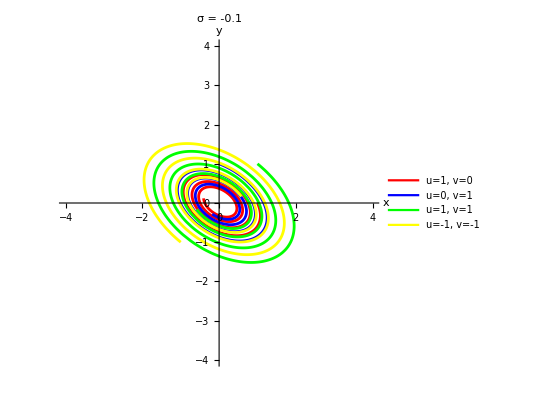

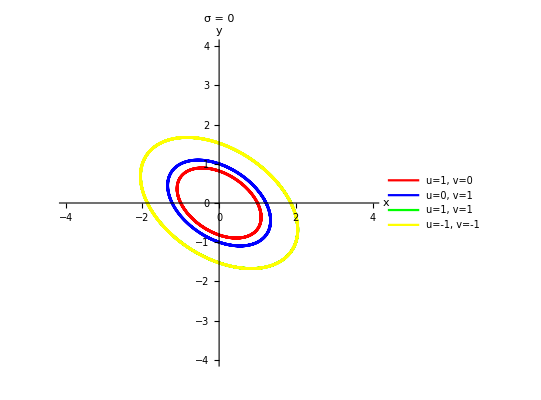

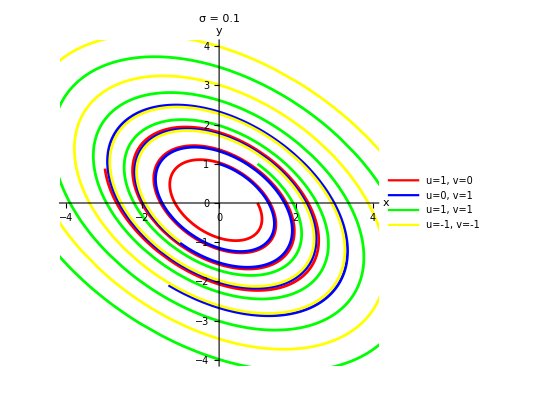

```mathematica
fx[sigma_, t_, u_, v_] :=  Exp[sigma*t] * (u * Cos[Sqrt[5]*t] + ( u  + 3*v)/Sqrt[5]*Sin[Sqrt[5]*t]) 
fy[sigma_, t_, u_, v_] :=  Exp[sigma*t] * (v * Cos[Sqrt[5]*t] - (2*u +  v )/Sqrt[5]*Sin[Sqrt[5]*t])

initialConditions = {
  {1, 0},  
  {0, 1},  
  {1, 1},
  {-1, -1}  
};
numberOfConditions = Length[initialConditions];

colors = {Red, Blue, Green, Yellow};
labels = Table[
   "u=" <> ToString[initialConditions[[i, 1]]] <> ", v=" <> ToString[initialConditions[[i, 2]]],
   {i, 1, numberOfConditions}
];

minx=-4;
miny=-4;
maxx=4;
maxy=4;

sigma = -0.1;
p1 = ParametricPlot[
   Evaluate[
     Table[
       {
         fx[sigma, t, initialConditions[[i, 1]], initialConditions[[i, 2]]],
         fy[sigma, t, initialConditions[[i, 1]], initialConditions[[i, 2]]]
       },
       {i, 1, numberOfConditions}
     ]
   ],
   {t, 0, 10},
   PlotRange -> {{minx, maxx}, {miny, maxy}},
   AxesLabel -> {x, y},
   PlotStyle -> colors,
   PlotLabel -> "σ = " <> ToString[sigma],
   PlotLegends -> LineLegend[colors, labels]
]

sigma = 0;
p2 = ParametricPlot[
   Evaluate[
     Table[
       {
         fx[sigma, t, initialConditions[[i, 1]], initialConditions[[i, 2]]],
         fy[sigma, t, initialConditions[[i, 1]], initialConditions[[i, 2]]]
       },
       {i, 1, numberOfConditions}
     ]
   ],
   {t, 0, 10},
   PlotRange -> {{minx, maxx}, {miny, maxy}},
   AxesLabel -> {x, y},
   PlotStyle -> colors,
   PlotLabel -> "σ = " <> ToString[sigma],
   PlotLegends -> LineLegend[colors, labels]
]

sigma = 0.1;	
p3 = ParametricPlot[
   Evaluate[
     Table[
       {
         fx[sigma, t, initialConditions[[i, 1]], initialConditions[[i, 2]]],
         fy[sigma, t, initialConditions[[i, 1]], initialConditions[[i, 2]]]
       },
       {i, 1, numberOfConditions}
     ]
   ],
   {t, 0, 10},
   PlotRange -> {{minx, maxx}, {miny, maxy}},
   AxesLabel -> {x, y},
   PlotStyle -> colors,
   PlotLabel -> "σ = " <> ToString[sigma],
   PlotLegends -> LineLegend[colors, labels]
]
```

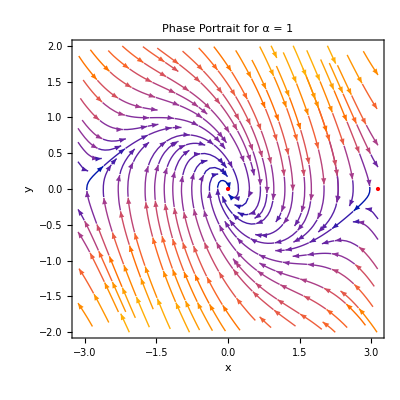

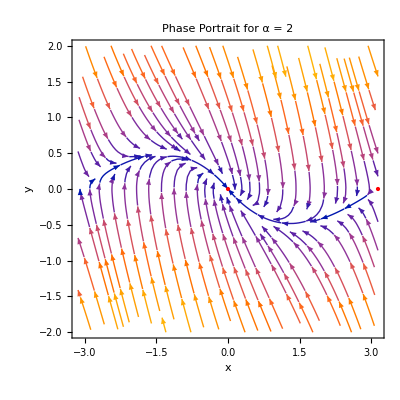

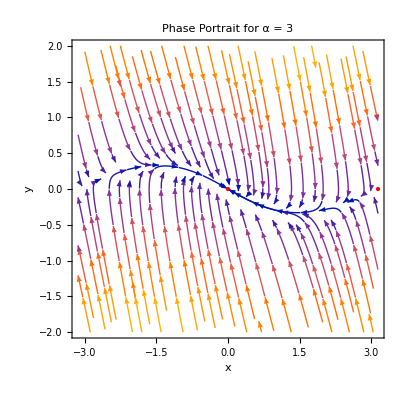

```mathematica
(* Define the system *)
pendulumSystem[x_, y_, alpha_] := {y, -Sin[x] - alpha y}

(* Parameters *)
alphaValues = {1, 2, 3}; (* Example values: below, at, and above critical damping *)

(* Plot for each alpha *)
Do[
 Module[{sol, plot},
  plot = StreamPlot[
    Evaluate[{y, -Sin[x] - alpha y}],
    {x, -Pi, Pi}, {y, -2, 2},
    StreamStyle -> Blue,
    FrameLabel -> {"x", "y"},
    PlotLabel -> Row[{"Phase Portrait for α = ", alpha}],
    Epilog -> {Red, PointSize[Large], Point[{0, 0}], Point[{Pi, 0}]}
  ];
  Print[plot]
 ],
 {alpha, alphaValues}
]
```

0.5

1

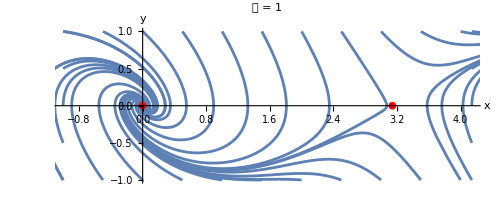

2

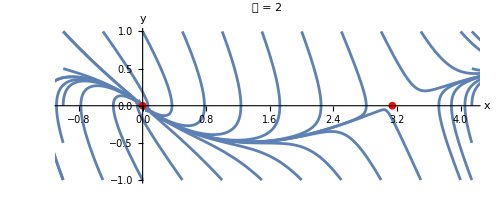

3

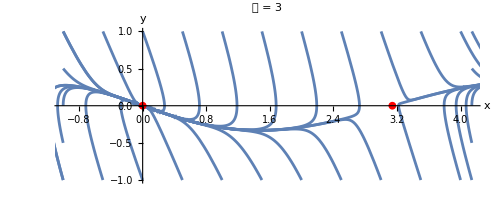

```mathematica
sol[x0_,y0_,alpha_] := NDSolve[{x'[t]== y[t], y'[t]== -Sin[x[t]] - alpha*y[t], x[0]==x0,y[0]==y0},{x,y},{t,0,10}]

minx=-1;
miny=-1;
maxx=Pi + 1;
maxy=1;

step = 0.5
initialC=Join[
			Table[{minx,y},{y,miny,maxy,step}],
			Table[{maxx,y},{y,miny,maxy,step}],
			Table[{x,miny},{x,minx,maxx,step}],
			Table[{x,maxy},{x,minx,maxx,step}]];
alpha = 1
p1=Show[
	Table[
		ParametricPlot[
			Evaluate[{x[t],y[t]}/. sol[initialC⟦i,1⟧, initialC⟦i,2⟧, alpha]],
			{t,0,10},
			PlotRange->{{minx,maxx},{miny,maxy}},
			AxesLabel->{x,y}
		]
		/. Line[x_]:>{Arrowheads[{{0.05, 0.5}, {0.05, 0.0}}],Arrow[x]},{i,1,Length[initialC]}
	], 
	ListPlot[{{Pi, 0}, {0, -0}}, 
		PlotStyle->{Red}, 
		PlotMarkers->{Automatic, 8}
	],
	PlotLabel -> "𝛼 = " <> ToString[alpha]
]

alpha = 2
p2=Show[
	Table[
		ParametricPlot[
			Evaluate[{x[t],y[t]}/. sol[initialC⟦i,1⟧, initialC⟦i,2⟧, alpha]],
			{t,0,10},
			PlotRange->{{minx,maxx},{miny,maxy}},
			AxesLabel->{x,y}
		]
		/. Line[x_]:>{Arrowheads[{{0.05, 0.5}, {0.05, 0.0}}],Arrow[x]},{i,1,Length[initialC]}
	], 
	ListPlot[{{Pi, 0}, {0, -0}}, 
		PlotStyle->{Red}, 
		PlotMarkers->{Automatic, 8}
	],
	PlotLabel -> "𝛼 = " <> ToString[alpha]
]
alpha = 3
p3=Show[
	Table[
		ParametricPlot[
			Evaluate[{x[t],y[t]}/. sol[initialC⟦i,1⟧, initialC⟦i,2⟧, alpha]],
			{t,0,10},
			PlotRange->{{minx,maxx},{miny,maxy}},
			AxesLabel->{x,y}
		]
		/. Line[x_]:>{Arrowheads[{{0.05, 0.5}, {0.05, 0.0}}],Arrow[x]},{i,1,Length[initialC]}
	], 
	ListPlot[{{Pi, 0}, {0, -0}}, 
		PlotStyle->{Red}, 
		PlotMarkers->{Automatic, 8}
	],
	PlotLabel -> "𝛼 = " <> ToString[alpha]
]
```